```mathematica
googleStock=QuantityMagnitude@FinancialData["GOOGL",{{2006,3,10},{2018,3,15},"Day"},"Value"];
```

```mathematica
params=FindDistributionParameters[googleStock,LogNormalDistribution[μ,σ]]
```

{μ→2.95202,σ→0.531241}

```mathematica
ml=LogLikelihood[LogNormalDistribution[μ,σ]/.params,googleStock]
```

-11308.7

```mathematica
llh1=LogLikelihood[LogNormalDistribution[mu,σ/.params],googleStock]
```

-9796.23-5359.35 (8.99665-5.90405 mu+mu^2)

```mathematica
llh2=LogLikelihood[LogNormalDistribution[μ/.params,s],googleStock]
```

-8929.87-426.854/s^2-3025 (1/2 (Log[2]+Log[π])+Log[s])

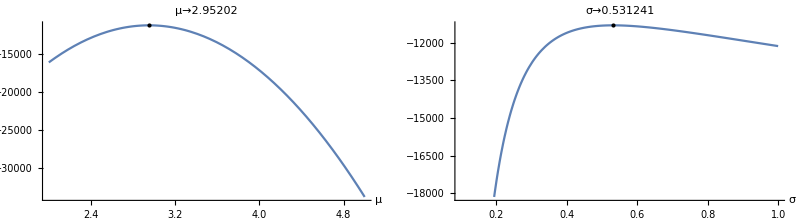

```mathematica
GraphicsRow[{Plot[llh1,{mu,2,5},Epilog->{PointSize[Large],Point[{μ/.params,ml}]},AxesLabel->{μ,None},PlotLabel->First[params]],Plot[llh2,{s,.1,1},Epilog->{PointSize[Large],Point[{σ/.params,ml}]},AxesLabel->{σ,None},PlotLabel->Last[params]]}]
```